# Effective potential for RSJJ potential+coloured noise:

```mathematica
Δ=noise/Sqrt[Subscript[f, 1]-2*Subscript[f, 2]]
```

noise/(√(f_1-2 f_2))

```mathematica
dV[ϕ_]=(Subscript[f, 1]*Sin[ϕ]+Subscript[f, 2]*Sin[2ϕ])(1+Δ*(Subscript[f, 1]*Cos[ϕ]+2*Subscript[f, 2]*Cos[2ϕ]))
```

(Sin[ϕ] f_1+Sin[2 ϕ] f_2) (1+(noise (Cos[ϕ] f_1+2 Cos[2 ϕ] f_2))/(√(f_1-2 f_2)))

```mathematica
(*Simplify[D[dV[ϕ],ϕ]]*)
```

Δ Cos[2 ϕ] f_1^2+Cos[ϕ] f_1 (1+Δ (-5+9 Cos[2 ϕ]) f_2)+2 f_2 (Cos[2 ϕ]+2 Δ Cos[4 ϕ] f_2)

```mathematica
Veff1=Integrate[dV[ϕ],ϕ]
```

(-noise Cos[2 ϕ] f_1^2-f_2 (2 Cos[2 ϕ] √(f_1-2 f_2)+noise Cos[4 ϕ] f_2)-4 Cos[ϕ] f_1 (√(f_1-2 f_2)-2 noise Sin[ϕ]^2 f_2))/(4 √(f_1-2 f_2))

```mathematica
Veff=Integrate[dV[ϕ],ϕ]/.{Subscript[f, 1]->6,Subscript[f, 2]->2,noise->2}
```

(-72 Cos[2 ϕ]-2 (2 √2 Cos[2 ϕ]+4 Cos[4 ϕ])-24 Cos[ϕ] (√2-8 Sin[ϕ]^2))/(4 √2)

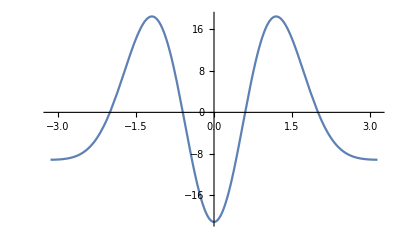

```mathematica
Plot[Veff,{ϕ,-Pi,Pi}]
```

```mathematica
effectivePotential=TrigReduce[Integrate[dV[ϕ],ϕ]]
```

1/(4 √(f_1-2 f_2))(-noise Cos[2 ϕ] f_1^2-4 Cos[ϕ] f_1 √(f_1-2 f_2)+2 noise Cos[ϕ] f_1 f_2-2 noise Cos[3 ϕ] f_1 f_2-2 Cos[2 ϕ] √(f_1-2 f_2) f_2-noise Cos[4 ϕ] f_2^2)

```mathematica
Simplify[Series[effectivePotential,{ϕ,π,6}]]
```

(f_1-(noise f_1^2)/(4 √(f_1-2 f_2))+1/4 f_2 (-2-(noise f_2)/(√(f_1-2 f_2))))-1/2 (√(f_1-2 f_2) (-noise f_1+√(f_1-2 f_2)+2 noise f_2)) (ϕ-π)^2+((f_1-8 f_2) (-4 noise f_1+√(f_1-2 f_2)+8 noise f_2) (ϕ-π)^4)/(24 √(f_1-2 f_2))+((16 noise f_1^2+32 f_2 (√(f_1-2 f_2)+32 noise f_2)-f_1 (√(f_1-2 f_2)+364 noise f_2)) (ϕ-π)^6)/(720 √(f_1-2 f_2))+O[ϕ-π]^7